## Investigating a Claim in No Extension of Quantum Theory by Colbeck and Renner (Nature Communications, 2 Aug 2011)

## Introduction

In their paper titled “No Extension of Quantum Theory” (Nature Communications, 2 Aug 2011), Colbeck and Renner make the following claim: 

“If X is a random variable with an arbitrary distribution, there exists a random variable X’ such that the joint distribution of [X,X’] is uniform.”

Inspired by Shalosh B. Ekhad (www.math.rutgers.edu/~zeilberg/pj.html), our goal is to investigate this claim using simulation. Can we find a simple example where given a discrete non-uniform distribution of X, we can specify a discrete distribution for X’ that will make the joint distribution of XX’ uniform?

We’ll take the case of an X that has 4 possible outcomes and a X’ that also has 4 possible outcomes and check the claim against about 7,500 candidate distributions for X’.

It’s worth stating up front that the approach taken here might lead to conclusions that are wrong. This might happen if: (1) We misinterpreted what Colbeck and Renner mean by the joint probability distribution of XX’, or (2) The set of candidates we are about to generate for the X’ distributions is not representative. There could be something amiss in the procedure for converting a randomly generated 4-tuple of Reals between 0 and 1 into a 4-tuple that meets the condition of a probability distribution -- i.e. that the sum of the elements of the 4-tuple add exactly to 1.
How do we use simulation to investigate the truth of a claim? Here’s the approach.

## Simulation Approach

### Step 1: Construct the random variables.

We have two discrete random variables, X and X’. X can take on values xVals = {a, b, c, d}, and X’ can take on values xprimeVals = {R, S, T, U}.

```mathematica
Clear[a,b,c,d,R,S,T];
```

```mathematica
xVals = {a,b,c};
xprimeVals = {R,S,T, U};
```

Joint probabilities of [X,X’] can then be defined on the following combinations of X and X’. Here are all possible outcomes of X,X’.

```mathematica
jointOutcomeSpace = Tuples[{xVals,xprimeVals}]
```

{{a,R},{a,S},{a,T},{a,U},{b,R},{b,S},{b,T},{b,U},{c,R},{c,S},{c,T},{c,U}}

When there are 3 values for X and 4 values for X’, the number of joint outcomes is 3 times 4 = 12. In general, the total number of distinct joint outcomes will be the number of possible outcomes for X multiplied by the number of possible outcomes for X’. We know that at the end of the day, the probability of each of the outcomes above will be 1/12th -- i.e. [X,X’] is uniformly distributed.

### Step 2: Assign X an arbitrary non-uniform discrete distribution.

Let pa be the probability of the outcome a, pb the probability of the outcome b and so on. Let’s pick some arbitraty values for pa, pb, pc, and pd.

```mathematica
pa = 0.2; pb = 0.3; pc = 0.5;
```

### Step 3: Simulate the Outcomes of X

We know the probabilities for outcomes a, b, and c (we picked these arbitrarily). Let’s generate a set of 20,000 outcomes of X. This will be the yardstick against which we measure the claim.

```mathematica
nTrials = 20000;
```

```mathematica
xOutcomes = RandomChoice[{pa, pb, pc} -> xVals, nTrials];
```

xOutcomes now holds the results of the 20,000 trials -- in other words, it is a list that has 20,000 elements where each element can be an a, b, c, or d. Here are the first 20 elements of that list:

```mathematica
Take[xOutcomes, 20]
```

{b,b,c,b,a,c,a,c,c,c,b,a,b,a,a,c,a,c,a,b}

### Step 4: Generate Candidate Probabilities for X’

According to Colbeck and Renner’s claim, there is some distribution of the outcomes of X’ such that the resulting joint distribution is uniform. So, in keeping with our simulation approach, let’s generate a bunch of 4-tuples of reals between 0 and 1 such that for every 4-tuple, its values add up to 1. We can use each of these 4-tuples to generate a set of 20,000 outcomes for X’. 

But let’s not get ahead of ourselves. In this section we focus on generating the candidate probabilities for the outcomes of X’.

```mathematica
(* The number of candidate X' distributions we are testing *)
nCandidates = 20000;
(* Generate a 4-tuple of Reals, each between 0 and 1 *)
candidates = Table[RandomReal[{0,1},4], {nCandidates}];
```

Of course not all such randomly generated 4-tuples will add up to exactly 1, which is what’s required if we need the 4-tuple to represent the probability of the 4 possible outcomes of X’. Let’s ensure that this is the case. We do so by taking the initial 4-tuple and finding the sum of the elements. If the sum is greater than 1, we subtract the overage from the largest element of the 4-tuple. If the sum is less than 1, we add the difference to the smallest element of the 4-tuple.

```mathematica
convertToProb2[fourTuple_]:= Module[{w,x,y,z,sum, maxPos, minPos},
(* Find the sum *)
{w,x,y,z} = fourTuple;
sum = Total[fourTuple];
(* Find the positions of the max and min value *)
maxPos = Flatten[Position[fourTuple, Max[fourTuple]]];
minPos = Flatten[Position[fourTuple, Min[fourTuple]]];
(* If the total is greater than 1, then subtract it from the largest element of the 4-tuple *)
If[sum > 1, Switch[maxPos[[1]],1,w=w-(sum-1),2,x=x-(sum-1),3,y = y-(sum -1), 4, z = z-(sum -1)]];
(* If the total is less than 1, then add it to the smallest element of the 3-tuple *)
If[sum < 1, Switch[minPos[[1]],1,w=w+(1-sum),2,x=x+(1-sum),3,y = y+(1-sum), 4, z = z + (1-sum)]];
(* If the sum is exactly 1, then just spit out the fourTuple *)
{w,x,y,z}
];
```

Even with this conversion we can sometimes get negative values for one of the elements of the 3-tuple. Delete these to form the set of all the candidate probability distributions for X’.

```mathematica
xPrimeProbs = DeleteCases[convertToProb2[#] & /@ candidates, {w_,x_,y_,z_}/; w ≤ 0 || x ≤0 || y≤ 0 || z≤ 0];
```

Let’s see how many candidates we’re testing:

```mathematica
numberCandidatesTested = Length[xPrimeProbs]
```

7258

Check to see if it’s working.

```mathematica
Take[Total[#] & /@ xPrimeProbs, -10];
```

Check to see how the probability values of the outcomes of X’ are distributed over the Interval [0,1].

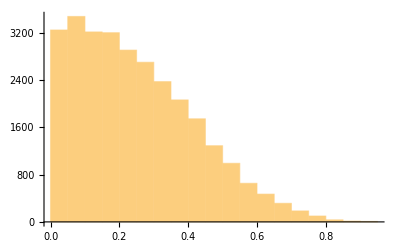

```mathematica
Histogram[Flatten[xPrimeProbs]]
```

This distribution makes sense; if you want four values to add to 1, and each value is obtained from a uniform distribution of reals between and including 0 and 1, then the frequencies of values greater than or equal to 0.4 should fall away as we see in the histogram above.

[INSTEAD, use a better function to generate the n-tuples]

```mathematica
genSingleTuple[tupleSize_, tupleSum_] := Module[{firstN, firstNTotal, outputTuple},
(* tuple size is self explanatory *)
(* tupleSum is the total to which the elements of the tuple should sum to *)
(* For most purposes, this sum will be 100 as in 100% *)
(* Generate the n-1 tuple; each element of the tuple can range between  *)
(* CAUTION: The function will return {} if the random numbers don't pan out. If that happens, try again! *)
firstN = RandomInteger[tupleSum,tupleSize - 1];
firstNTotal = Total[firstN];
If[firstNTotal ≤ tupleSum, outputTuple = Append[firstN, tupleSum-firstNTotal], outputTuple = {}]
];
```

```mathematica
genSingleTuple[3,100]
```

{}

```mathematica
genMultipleTuples[tupleSize_, tupleSum_, numTuples_]:= Module[{},
(* NOTE: Because some of the tuples generated by genSingleTuple will be {}, numTuples should be a much larger number than the actual number of tuples that are required. Think of numTuples as the maximum possible tuples that can be generated but usually the actual number will be much less. *)
Table[genSingleTuple[tupleSize, tupleSum], numTuples] /. {} -> Sequence[]
];
```

```mathematica
scaleMaxMin[tupleSize_, tupleSum_, numTuples_, scalingFactors_]:= Module[{sampleTuples, scaledTuples, scaledTuplesTotals},
(* tupleSize, tupleSum, numTuples are all inputs of genMultipleTuples *)
(* scalingFactors are the multipliers for each point on the scale. They appear as a series of numbers in the form {-5, -1, 3, 9}, for example. *)
(* If tupleSize ≠ Length[scalingFactors], then generate an error message *)
If[tupleSize ≠ Length[scalingFactors], Return["The number of scaling factors should be the same as the tuple size. Please try again."]];
(* Generate the multiple tuples *)
sampleTuples = genMultipleTuples[tupleSize, tupleSum, numTuples];
(* Multiply each tuple by the scaling factors *)
scaledTuples = scalingFactors * # & /@ sampleTuples;
(* Total up each scaled tuple *)
scaledTuplesTotals = Total[#] & /@scaledTuples;
(* Output the Max and Min of the scaledTuplesTotals *)
{Max[scaledTuplesTotals], Min[scaledTuplesTotals]}
];
```

```mathematica
scaleMaxMin[4, 100, 100000, {-5,-1,3,9}]
```

{884,-492}

```mathematica
xprimeTuples = genMultipleTuples[4,100,300000];
```

```mathematica
Length[xprimeTuples]
```

51347

```mathematica
Take[xprimeTuples,10]
```

{{10,61,6,23},{19,32,2,47},{42,17,27,14},{17,28,27,28},{2,33,42,23},{8,59,6,27},{0,10,72,18},{13,21,29,37},{29,7,32,32},{29,26,13,32}}

Let’s check on how these xprimeTuples are distributed. Ideally, each element of the tuple should be uniformly distributed from 1 to 100.

What’s the distribution of the each of the elements of the tuples?

```mathematica
{t1, t2, t3, t4} = Transpose[xprimeTuples];
```

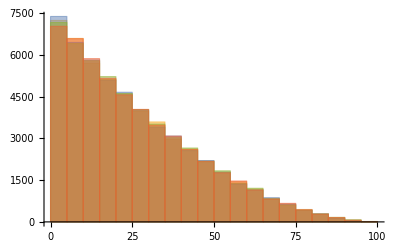

```mathematica
dt = Histogram[{t1,t2,t3,t4}]
```

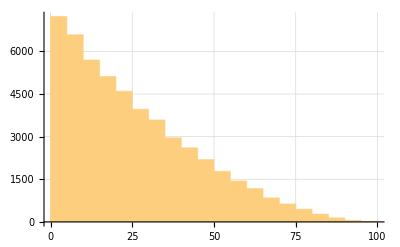

```mathematica
dt1 = Histogram[t1,GridLines->Automatic]
```

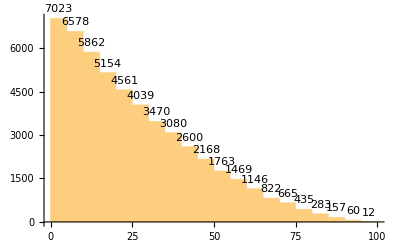

```mathematica
dt4 = Histogram[t4, LabelingFunction -> Above]
```

Each element is distributed similarly, but he distribution is far from uniform: there are many more smaller values than there are larger values at any location of the tuple.

Now, let’s convert these to probabilities.

```mathematica
xprimeProbs = #/100. & /@ xprimeTuples;
```

```mathematica
Take[xprimeProbs, -10]
```

{{0.36,0.22,0.03,0.39},{0.23,0.18,0.43,0.16},{0.04,0.92,0.03,0.01},{0.09,0.15,0.19,0.57},{0.54,0.13,0.32,0.01},{0.83,0.01,0.06,0.1},{0.22,0.12,0.43,0.23},{0.12,0.76,0.01,0.11},{0.24,0.59,0.08,0.09},{0.16,0.34,0.17,0.33}}

OK, we’re ready to test each of these distributions.

## Testing

For the testing phase, we’ll pretend as if the {a, b, c}’s are in one urn and the {R, S, T, U}’s are in another urn. The tokens in each urn are distributed according to the given distributions - the one for the first urn will remain the same throughout; the one for the second urn will change as we try each of the distributions we’ve manufactured in xprimeProbs.

```mathematica
urn1Population = xOutcomes;
```

```mathematica
(* CAUTION: This creates about 10,000 sets of 20,000 xprimeVals - WOW! *)
(* The complete xprimeProbs contains about 52,000 elements *)
urn2Populations= RandomChoice[# -> xprimeVals, nTrials] & /@ Take[xprimeProbs, 10000];
```

Now randomly choose 1 token from urn 1 and 1 token from urn 2; do this 10,000 times and see what the joint distribution is. And do this for every candidate distribution we’ve generated for X’.

```mathematica
(* CAUTION: This creates 10,000 sets of 12 values and does 10,000 tests on top of that -- VERY TIME CONSUMING. RUN INFREQUENTLY *)
testDistributions = Table[(Count[Table[{RandomChoice[xOutcomes], RandomChoice[urn2Populations[[i]]]}, 10000], #] & /@ jointOutcomeSpace) / 10000., {i,1,10000}];
```

```mathematica
requiredDistribution = Table[1/12., 12]
```

{0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333,0.0833333}

What’s the Euclidean distance between each of the testDistributions and the required Distribution?

```mathematica
euclid = EuclideanDistance[#, requiredDistribution] & /@ testDistributions;
```

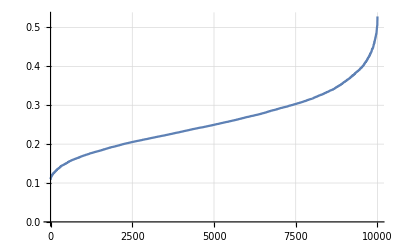

```mathematica
ListLinePlot[Sort[euclid], GridLines->Automatic]
```

There are a range of distances and some of them are quite close. Let’s see which xprimeProbs result in low distances.

```mathematica
minED = Min[euclid]
```

0.109406

```mathematica
minxprimeProbs = xprimeProbs[[Flatten[Position[euclid, minED]]]]
```

{{0.26,0.27,0.24,0.23}}

```mathematica
xprimeProbs[[Flatten[Position[euclid, x_ /; x ≥ minED && x≤ minED+0.01]]]]
```

{{0.2,0.27,0.29,0.24},{0.28,0.22,0.25,0.25},{0.32,0.24,0.22,0.22},{0.24,0.31,0.24,0.21},{0.22,0.27,0.25,0.26},{0.24,0.26,0.25,0.25},{0.28,0.23,0.23,0.26},{0.24,0.2,0.28,0.28},{0.3,0.26,0.22,0.22},{0.23,0.26,0.31,0.2},{0.31,0.25,0.24,0.2},{0.2,0.28,0.25,0.27},{0.28,0.24,0.26,0.22},{0.3,0.23,0.27,0.2},{0.23,0.28,0.24,0.25},{0.26,0.27,0.26,0.21},{0.26,0.22,0.27,0.25},{0.19,0.27,0.29,0.25},{0.24,0.27,0.27,0.22},{0.24,0.21,0.29,0.26},{0.24,0.25,0.24,0.27},{0.28,0.19,0.25,0.28},{0.22,0.23,0.24,0.31},{0.19,0.29,0.27,0.25},{0.19,0.25,0.3,0.26},{0.28,0.26,0.21,0.25},{0.24,0.24,0.26,0.26},{0.3,0.24,0.19,0.27},{0.26,0.27,0.24,0.23},{0.23,0.3,0.24,0.23},{0.23,0.25,0.23,0.29},{0.3,0.28,0.2,0.22},{0.26,0.22,0.29,0.23},{0.3,0.27,0.24,0.19},{0.29,0.26,0.22,0.23},{0.29,0.22,0.25,0.24},{0.26,0.19,0.27,0.28},{0.29,0.26,0.26,0.19},{0.18,0.26,0.28,0.28},{0.27,0.2,0.31,0.22},{0.27,0.24,0.25,0.24},{0.22,0.21,0.28,0.29},{0.26,0.31,0.19,0.24},{0.26,0.29,0.25,0.2},{0.29,0.24,0.23,0.24},{0.24,0.28,0.24,0.24}}

### Test a Candidate Probability Distribution for X’

Take the first value of xPrimeProbs. Generate nTrials representing a measurement of X’ nTrials times.

```mathematica
xPrimeOutcomes = RandomChoice[xPrimeProbs[[1]] -> xprimeVals, nTrials];
```

Create the set of joint outcomes XX’

```mathematica
jointDistribution = Transpose[{xOutcomes, xPrimeOutcomes}];
```

Count the number of times each combination of X and X’ outcomes in the jointOutcomeSpace occurs and divide each count by the number of trials to calculate a probability of occurrence of that joint outcome.

```mathematica
jointOutcomeProbs = N[Count[jointDistribution, #]/nTrials] & /@ jointOutcomeSpace
```

{0.02375,0.06905,0.0936,0.0158,0.0372,0.10105,0.13745,0.02375,0.01835,0.0535,0.06805,0.0116,0.0407,0.1186,0.1593,0.02825}

For this joint distribution to be uniform the joinOutcomeProbs must be equal. The value each of the joint outcomes must satisfy is the reciprocal of the number of possible outcomes of X times the number of possible outcomes for X’. In this case,

```mathematica
uniformP = 1./16.;
```

```mathematica
uniformProbs = Table[uniformP, {16}]
```

{0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625,0.0625}

Now measure how far away these jointOutcomeProbs are from the required joint probabilities for a uniform joint distribution. There are a handful of options that make sense for measuring distance. One distance measure is Euclidean distance which is defined as:

```mathematica
EuclideanDistance[{a,b,c, d},{w,x,y,z}]
```

√(Abs[a-w]^2+Abs[b-x]^2+Abs[c-y]^2+Abs[d-z]^2)

Another example is Bray-Curtis distance which is defined as:

```mathematica
BrayCurtisDistance[{a,b,c, d},{w,x,y,z}]
```

(Abs[a-w]+Abs[b-x]+Abs[c-y]+Abs[d-z])/(Abs[a+w]+Abs[b+x]+Abs[c+y]+Abs[d+z])

The Euclidean distance between a list and itself should be zero as we expect.

```mathematica
euclideanD = EuclideanDistance[uniformProbs, uniformProbs]
```

0.

The Euclidean distance between the joint outcome probabilities based on our candidate distribution for X’ is:

```mathematica
euclideanD = EuclideanDistance[jointOutcomeProbs, uniformProbs]
```

0.187087

The same relations hold for the Bray-Curtis distances.

```mathematica
braycurtisD = BrayCurtisDistance[uniformProbs, uniformProbs]
```

0.

```mathematica
braycurtisD = BrayCurtisDistance[jointOutcomeProbs, uniformProbs]
```

0.3096

The Bray-Curtis distance is higher than the Euclidean distance (0.3096 versus 0.1871) but it doesn’t matter which one we pick as long as we’re consistent. For our purposes, let’s stick with the Euclidean distance.

### Test All Candidate X’ Distributions

For a given distance measure, the goal is to find distances between jointOutcomeProbs -- the probabilities generated by the candidate probabilities for X’ -- and uniformProbs. Let’s use the Euclidean distance as our measure of distance between jointOutcomeProbs and uniformProbs.

Let’s find the Euclidean distance between uniformProbs and the XX’ distributions generated by each candidate distribution of X’.

```mathematica
xPrimeOutcomesAll = RandomChoice[# -> xprimeVals, nTrials]& /@ xPrimeProbs;
```

```mathematica
jointDistributionAll = Transpose[{xOutcomes,#}] & /@  xPrimeOutcomesAll;
```

```mathematica
jointOutcomeProbsAll = Table[N[Count[jointDistributionAll[[i]], #]/nTrials] & /@ jointOutcomeSpace, {i, 1, Length[jointDistributionAll]}];
```

```mathematica
euclideanDAll = EuclideanDistance[#, uniformProbs] & /@ jointOutcomeProbsAll;
```

Here is the plot of Euclidean distances for each of the candidate X’ distributions we’ve tried.

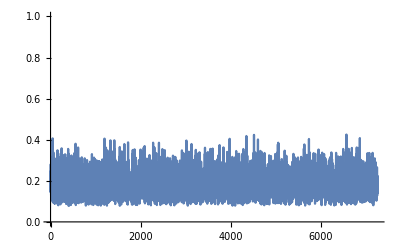

```mathematica
gED = ListLinePlot[euclideanDAll, PlotRange-> {0,1}]
```

## Analysis

We’ve tested about 7,250 candidate probability distributions for X’. The graphs above show that none of the distances is zero, and hence that none of these distributions for X’ make the joint probability distribution uniform. Now this doesn’t disprove Colbeck and Renner’s claim, but it should give us pause. (And look on the bright side -- there seems to be a limit to how far off you can be from a uniform distribution -- the plots have a clear upper bound too!)

### The Minimum Distance and Its Vicinity

Let’s focus on Euclidean distance and see which probability distributions for X’ resulted in the smallest distance from the uniform distribution.

```mathematica
minED = Min[euclideanDAll]
```

0.0776811

In our generation of about 7,250 candidate distributions for X’, this minimum value occurred in the following position:

```mathematica
minEDPos = Position[euclideanDAll, minED]
```

{{403}}

So now we can see which probability distribution for X’, i.e., {p(R), p(S), p(T)}, generates this minimum distance. The X’ distribution that is the closest to giving us a uniform XX’ distribution is:

```mathematica
minProb = xPrimeProbs[[Position[euclideanDAll, minED][[1]][[1]]]]
```

{0.255673,0.241771,0.247019,0.255537}

We can see from the above X’ distribution that it is pretty close to being uniform. Later we’ll try the uniform case for X’ to see if it indeed generates a uniform XX’.

To get a better sense of how the distributions of XX’ behave, let’s find some of the probability distributions around the minimum distance value. To be more precise, where are the values that are within 0.001 of the minimum distance?

```mathematica
minProbsPos = Flatten[Position[euclideanDAll, x_ /; x ≥ minED && x≤ minED+0.001]]
```

{403,1538}

```mathematica
minProbs = xPrimeProbs[[#]] & /@ minProbsPos
```

{{0.255673,0.241771,0.247019,0.255537},{0.249504,0.269174,0.225121,0.256201}}

And how close to uniform are the joint probability distributions generated by these probability distributions for X’?

```mathematica
minJointProbs = jointOutcomeProbsAll[[#]] & /@ minProbsPos
```

{{0.0525,0.0481,0.0505,0.0511,0.07775,0.07135,0.07665,0.0737,0.03745,0.03565,0.03815,0.04025,0.089,0.0822,0.08595,0.0897},{0.04885,0.0548,0.0462,0.05235,0.07505,0.07605,0.07015,0.0782,0.0366,0.04115,0.035,0.03875,0.08605,0.09175,0.07935,0.0897}}

Not that uniform -- some of the joint outcomes are more than twice as likely as some others in each of these joint distributions. Nevertheless, in picking distributions for X’ we should stick as closely as we can to the minProbs values above.

### The Maximum Distance and Its Vicinity

Which distributions for X’ should we avoid? Obviously the ones that generate the biggest distances from the required uniform distribution.

```mathematica
maxED = Max[euclideanDAll]
```

0.425197

```mathematica
maxEDPos = Position[euclideanDAll, maxED]
```

{{6569}}

Which probability distribution for X’, i.e., {p(R), p(S), p(T)}, generates this maximum distance?

```mathematica
maxProb = xPrimeProbs[[Position[euclideanDAll, maxED][[1]][[1]]]]
```

{0.0320519,0.94515,0.00404916,0.0187492}

We see immediately that this is a very imbalanced X’ distribution. The probability of outcome S swamps all the other probabilities by at least an order of magnitude.

What are some of the probability distributions around the maximum distance value? To be more precise, where are the values that are within 0.02 of the maximum value?

```mathematica
maxProbsPos = Flatten[Position[euclideanDAll, x_ /; x ≤  maxED && x≥  maxED-0.02]]
```

{47,1198,4348,4517,6569,6867}

```mathematica
maxProbs = xPrimeProbs[[#]] & /@ maxProbsPos
```

{{0.0117144,0.000712396,0.0796145,0.907959},{0.0440982,0.910882,0.0150494,0.02997},{0.0102035,0.0314936,0.930919,0.0273842},{0.0192988,0.0294301,0.0107897,0.940481},{0.0320519,0.94515,0.00404916,0.0187492},{0.0157914,0.00135166,0.0718255,0.911031}}

It’s apparent that the distributions that are far away from the required uniform distribution are highly imbalanced -- there is one very large probability value around 0.9 and the other three probabilities are consequently very small. 

And finally, what kinds of distributions are generated for XX’ when we use these highly imbalanced distributions for X’?

```mathematica
maxJointProbs = jointOutcomeProbsAll[[#]] & /@ maxProbsPos
```

{{0.0021,0.,0.0162,0.1839,0.00335,0.00005,0.02445,0.2716,0.002,0.0001,0.0109,0.1385,0.0036,0.00025,0.028,0.315},{0.00855,0.18445,0.00345,0.00575,0.0137,0.2705,0.00445,0.0108,0.00645,0.13885,0.0017,0.0045,0.0151,0.31535,0.00545,0.01095},{0.0019,0.00655,0.1886,0.00515,0.0037,0.00925,0.278,0.0085,0.0011,0.00435,0.1421,0.00395,0.0031,0.01185,0.3221,0.0098},{0.00325,0.006,0.0018,0.19115,0.00625,0.00905,0.0033,0.28085,0.00315,0.0053,0.00125,0.1418,0.00655,0.01065,0.00395,0.3257},{0.0058,0.19075,0.0006,0.00505,0.0109,0.28055,0.0012,0.0068,0.00445,0.14345,0.0006,0.003,0.01105,0.3274,0.00125,0.00715},{0.00335,0.0003,0.01455,0.184,0.0048,0.00055,0.0206,0.2735,0.0023,0.00015,0.01025,0.1388,0.00585,0.0005,0.0249,0.3156}}

Again, we can see that each of the above are nowhere near uniform.

## One More Test

Our analysis has pointed us in the direction of a potential answer. Perhaps the probability distribution for X’ that produces a zero distance, i.e., a uniformly distributed XX’ is simply a uniform distribution of X’. In this case, that distribution will be X’ = {0.25, 0.25, 0.25, 0.25}. 

Let’s try this out.

```mathematica
xTest = RandomChoice[{pa, pb, pc, pd} -> {a, b, c, d}, nTrials];
```

```mathematica
xPrimeTest = RandomChoice[{0.25, 0.25, 0.25,0.25} -> {R, S, T,U}, nTrials];
```

```mathematica
jointTest = Transpose[{xTest, xPrimeTest}];
```

```mathematica
testjointOutcomeProbs = N[Count[jointTest, #]/nTrials] & /@ jointOutcomeSpace
```

{0.04795,0.04705,0.0512,0.0488,0.0748,0.0735,0.07515,0.07775,0.03885,0.0365,0.0389,0.0352,0.0909,0.08985,0.0889,0.0847}

```mathematica
testEuclideanD = EuclideanDistance[testjointOutcomeProbs, uniformProbs]
```

0.0819305

Unfortunately, just making the X’ a uniform distribution won’t work.

## Conclusion and Caveats

The simulation approach we’ve taken is limited and nothing definitive can be said (without a lot more work) about the truth of Colbeck and Renner’s claim. However, the simulations do give us a feel for how the distributions behave in the simple case that we’ve considered where X has the outcomes {a, b, c, d} and X’ has the outcomes {R, S, T, U}. Based on our evidence it doesn’t seem likely that there is an X’ distribution that will make the joint distribution of XX’ uniform. Clearly, an uniform distribution for X’ isn’t the solution, nor are any of the 7,250 or so other distributions we’ve tried. 

Therefore, for the simple case we’ve constructed, the evidence generated by the simulations points to the claim being false. The best cases for constructing the X’ probabilities is to keep them balanced and roughly equal (but making them exactly equal is not a solution).  And given the pattern we’ve seen developing with the distances, it would be surprising to see how increasing the number of outcomes of X or of X’ will make it any better for the claim.

That said, our conclusion is still tentative and might be wrong as we mentioned right up front for one or more of the following reasons: (1) We misinterpreted what Colbeck and Renner mean by the joint probability distribution of XX’, or (2) The set of candidates we generated for the X’ distributions is not representative or simply didn’t include the distribution that would have satisfied the claim. This might be the case because there might be something amiss in the procedure for converting a randomly generated 4-tuple of Reals between 0 and 1 into a 4-tuple that meets the condition of a probability distribution -- i.e. that the sum of the elements of the 4-tuple add exactly to 1.

Nevertheless, our simulations have given us some important information about how joint probability distributions behave.